```mathematica
IntLog[n_]:=Module[{l=FactorInteger[n]},If[n!=1,Return[Sum[l[[i,1]]*l[[i,2]],{i,Length[l]}]],Return[0]]]

n=100000;
d=20;
myIntLogs=Table[IntLog[i],{i,1,n}];
myIntLogsDivLinear=myIntLogs/Range[n];
myLogIntLogs=Map[Log[2,#]&,myIntLogs];
recHolders={2};
For[i=2,i<n,i++,
If[myIntLogsDivLinear[[i]]<IntLog[recHolders[[-1]]]/recHolders[[-1]],AppendTo[recHolders,i]]
]
r=Length[recHolders];
myRecHolders={Range[r],recHolders,Map[myIntLogs[[#]]&,recHolders],Map[myIntLogs[[#]]/#&,recHolders],Map[myIntLogs[[#]]/Log[2,#]&,recHolders]}ᵀ;
```

```mathematica
TableForm[Table[{i,IntLog[i]},{i,1,d}]]
```

1 | 0
2 | 2
3 | 3
4 | 4
5 | 5
6 | 5
7 | 7
8 | 6
9 | 6
10 | 7
11 | 11
12 | 7
13 | 13
14 | 9
15 | 8
16 | 8
17 | 17
18 | 8
19 | 19
20 | 9

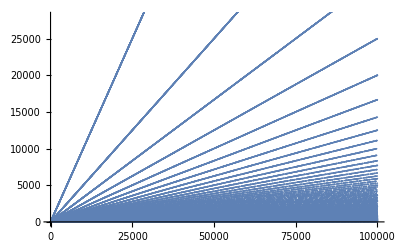

```mathematica
ListPlot[myIntLogs]
```

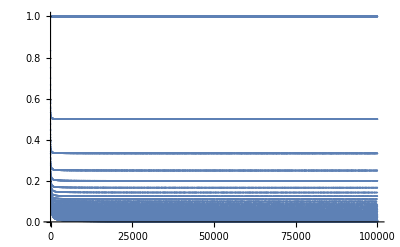

```mathematica
ListPlot[myIntLogsDivLinear]
```

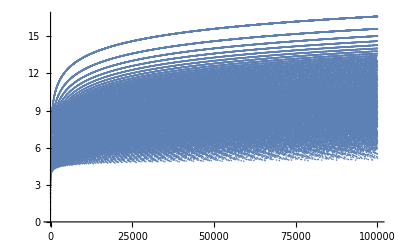

```mathematica
ListPlot[myLogIntLogs]
```

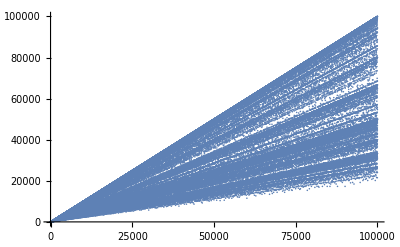

```mathematica
ListPlot[Table[EulerPhi[i],{i,n}]]
```

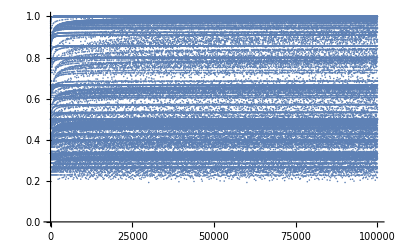

```mathematica
ListPlot[Table[EulerPhi[i]/i,{i,n}]]
```

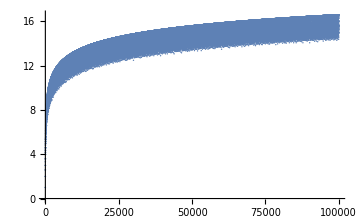

```mathematica
ListPlot[Table[Log[2,EulerPhi[i]],{i,n}]]
```

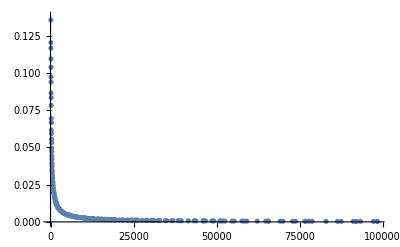

```mathematica
ListPlot[myRecHoldersᵀ[[{2,4}]]ᵀ]
```

```mathematica
TableForm[Take[N[myRecHolders],d]]
```

1. | 2. | 2. | 1. | 2.
2. | 6. | 5. | 0.833333 | 1.93426
3. | 8. | 6. | 0.75 | 2.
4. | 9. | 6. | 0.666667 | 1.89279
5. | 12. | 7. | 0.583333 | 1.9526
6. | 15. | 8. | 0.533333 | 2.04766
7. | 16. | 8. | 0.5 | 2.
8. | 18. | 8. | 0.444444 | 1.9185
9. | 24. | 9. | 0.375 | 1.96294
10. | 27. | 9. | 0.333333 | 1.89279
11. | 32. | 10. | 0.3125 | 2.
12. | 36. | 10. | 0.277778 | 1.93426
13. | 40. | 11. | 0.275 | 2.06692
14. | 45. | 11. | 0.244444 | 2.00297
15. | 48. | 11. | 0.229167 | 1.96957
16. | 54. | 11. | 0.203704 | 1.91142
17. | 60. | 12. | 0.2 | 2.03153
18. | 64. | 12. | 0.1875 | 2.
19. | 72. | 12. | 0.166667 | 1.94492
20. | 80. | 13. | 0.1625 | 2.05633

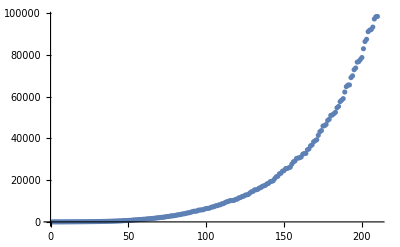

```mathematica
ListPlot[myRecHoldersᵀ[[2]]ᵀ]
```

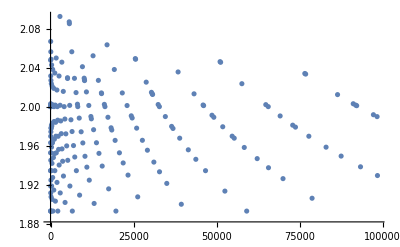

```mathematica
ListPlot[myRecHoldersᵀ[[{2,5}]]ᵀ]
```

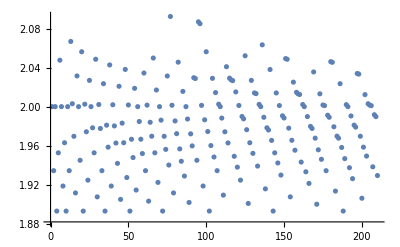

```mathematica
ListPlot[myRecHoldersᵀ[[5]]ᵀ]
```

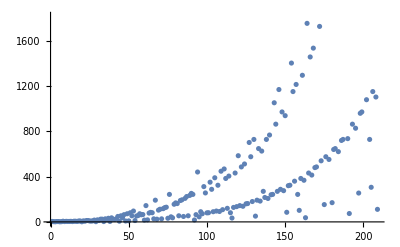

```mathematica
Δ[l_]:=Module[{i,res={}},
For[i=2,i<=Length[l],i++,
AppendTo[res,l[[i]]-l[[i-1]]]
];
Return[res]
]
ListPlot@Δ[recHolders]
```